## Dual control calculations (Tonk & Kappen) (Prob. 10.21)

Simple 2 - stage example

```mathematica
Clear["Global`*"];
```

At stage 1

```mathematica
J1u=(1+β)/2((x0+u0)^2+ξ^2)+(1-β)/2((x0-u0)^2+ξ^2)+R u0^2 // Simplify
```

(1+R) u0^2+x0^2+2 u0 x0 β+ξ^2

```mathematica
Minimize[{J1u,R>0},u0]//Simplify
```

{Piecewise[{{(x0^2 (1+R-β^2))/(1+R)+ξ^2, R>0}, {∞, True}}],{u0→Piecewise[{{-(x0 β)/(1+R), R>0}, {Indeterminate, True}}]}}

```mathematica
J1u/.u0->-(x0 β)/(1+R)//FullSimplify
```

x0^2 (1-β^2/(1+R))+ξ^2

At stage 2

```mathematica
f=1/2 ((x0+u0+ξ0)^2(Tanh[u0(u0+ξ0)])^2+(x0-u0+ξ0)^2(Tanh[u0(-u0+ξ0)])^2);
```

```mathematica
Series[Tanh[x],{x,0,4}]
```

x-x^3/3+O[x]^5

```mathematica
f1=Series[f,{u0,0,4}]
```

ξ0^2 (x0+ξ0)^2 u0^2+1/2 (2 ξ0^2+8 ξ0 (x0+ξ0)+2 (x0+ξ0)^2 (1-(2 ξ0^4)/3)) u0^4+O[u0]^5

```mathematica
f1/.x0->0
```

ξ0^4 u0^2+1/2 (10 ξ0^2+2 ξ0^2 (1-(2 ξ0^4)/3)) u0^4+O[u0]^5

```mathematica
f2=Collect[Expectation[f1,ξ0\[Distributed]NormalDistribution[0,1]],u0]
```

u0^4 (-4-x0^2)+u0^2 (3+x0^2)

```mathematica
Collect[f2/.x0->0//Simplify,u0]
```

3 u0^2-4 u0^4

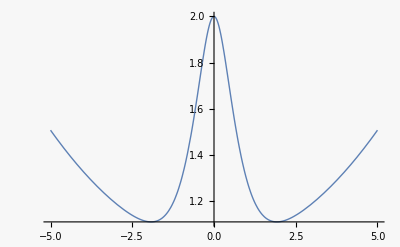

```mathematica
J0u=(1+R)u0^2-f/(R+1)+2;
Plot[NExpectation[J0u/.{R->0.01,x0->0},ξ0\[Distributed]NormalDistribution[0,1]],{u0,-5,5},PlotRange->All]
```

```mathematica
J0us=Collect[Expectation[Series[J0u,{u0,0,4}],ξ0\[Distributed]NormalDistribution[0,1]],u0]
```

(2+2 R)/(1+R)+(u0^2 (-2+2 R+R^2-x0^2))/(1+R)+(u0^4 (4+x0^2))/(1+R)

```mathematica
J00=J0us/.{x0->0,u0->√((-(-2+2 R+R^2))/8)}//Simplify
```

-(-28-40 R+4 R^3+R^4)/(16 (1+R))

Now compute the exact u numerically

```mathematica
dR=0.1;  (* best to use dR=0.001;    
timing on macbook pro 2019 is 17.6 s for 0.1 *)
dataAll=ParallelTable[FindMinimum[{NExpectation[J0u/.x0->0,ξ0\[Distributed]NormalDistribution[0,1]],u0>=0},{u0,0}],{R,1,dR,-dR}];//AbsoluteTiming
```

{17.5261,Null}

Export data

```mathematica
J0dat = First /@ dataAll;
u0dat=u0/.Last /@ dataAll;
dat={Range[1,0.001,-0.001],u0dat,J0dat}//Transpose//TableForm ;
(* 
SetDirectory[NotebookDirectory[]];
Export["alldat.dat",dat]; 
*)
```

Transpose::nmtx: The first two levels of {{1.,0.999,0.998,0.997,0.996,0.995,0.994,0.993,0.992,0.991,«990»},{«21»,«8»,«19»},{2.,2.,2.,1.99954,1.99115,1.96882,1.92624,1.85309,1.73069,1.51742}} cannot be transposed.

Look at the large-R limit

```mathematica
Series[((y-1/y)/(y+1/y))^2,{y,-∞,4}]
```

1-4/y^2+8/y^4+O[1/y]^5

Mathematica can't expand Tanh[x]^2 for some reason, so above is closest, with y=ⅇ^x

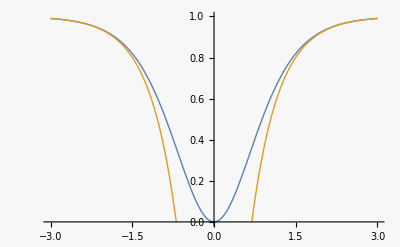

```mathematica
Plot[{Tanh[x]^2,1-4 ⅇ^(-2Abs[x])},{x,-3,3},PlotRange->{0,1}]
```

```mathematica
f0 = (1-4 ⅇ^(-2 u0^2))(u0^2+1);
j0=Collect[2+(1+R) u0^2-f0/(1+R),u0]
```

2-1/(1+R)+(4 ⅇ^(-2 u0^2))/(1+R)+(1+R-1/(1+R)+(4 ⅇ^(-2 u0^2))/(1+R)) u0^2

```mathematica
j0s=Series[j0,{R,0,1}]//FullSimplify
```

(1+4 ⅇ^(-2 u0^2) (1+u0^2))+(1+2 u0^2-4 ⅇ^(-2 u0^2) (1+u0^2)) R+O[R]^2

Now allow for initial bias (β_0≠ 0)

```mathematica
ff0=(1+β0)/2 ((x0+u0+ξ0)^2(Tanh[u0(u0+ξ0)])^2)+(1-β0)/2 ((x0-u0+ξ0)^2(Tanh[u0(-u0+ξ0)])^2);
```

```mathematica
ff1=Series[ff0,{u0,0,4}]
```

(x0^2 ξ0^2+2 x0 ξ0^3+ξ0^4) u0^2+2 (x0^2 β0 ξ0+3 x0 β0 ξ0^2+2 β0 ξ0^3) u0^3+1/3 (3 x0^2+18 x0 ξ0+18 ξ0^2-2 x0^2 ξ0^4-4 x0 ξ0^5-2 ξ0^6) u0^4+O[u0]^5

```mathematica
ff1avg=Expectation[ff1,ξ0\[Distributed]NormalDistribution[0,1]]
```

u0^2 (3+x0^2-u0^2 (4+x0^2)+6 u0 x0 β0)

```mathematica
Collect[ff1avg,u0]
```

u0^4 (-4-x0^2)+u0^2 (3+x0^2)+6 u0^3 x0 β0

```mathematica
ff0a=(1+β0)/2 ((x0+u0+ξ0)^2(Tanh[u0(u0+ξ0)])^2);
ff0aavg=Expectation[Series[ff0a,{u0,0,4}],ξ0\[Distributed]NormalDistribution[0,1]]
```

-1/2 u0^2 (-3-6 u0 x0-x0^2+u0^2 (4+x0^2)) (1+β0)

```mathematica
Collect[ff0aavg,u0]
```

3 u0^3 x0 (1+β0)-1/2 u0^2 (-3-x0^2) (1+β0)-1/2 u0^4 (4+x0^2) (1+β0)